```mathematica
cap=1;
Vna=115;
Vk=-12;
Vl=10.6;
Gna=120;
Gk=36;
Gl=0.3;

sde=0.5;
sre=3;
sdi=0.5;
sri=7;
Vge=65;
Vgi=-15;
fe=0.04;
fi=0.04;
see=0.05;
sii=0;

fan[v_]:=(0.1-0.01 v)/(Exp[1-0.1 v]-1)
fam[v_]:=(2.5-0.1 v)/(Exp[2.5-0.1 v]-1)
fah[v_]:=0.07 Exp[-v/20]
fbn[v_]:=0.125 Exp[-v/80]
fbm[v_]:=4 Exp[-v/18]
fbh[v_]:=1/(Exp[3-0.1 v]+1)

Clear[T,I1ext,SimuHHcurrent]
SimuHHcurrent[innerI1ext_,innerT_]:=
Module[{I1ext=innerI1ext,T=innerT},
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl+I1ext[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
V1[0]==0.00027756626542950875,
m1[0]==0.052934217620863984,
h1[0]==0.5961110463468279,
n1[0]==0.31768116757978115
},{V1,m1,h1,n1},{t,0,T},
Method->"ImplicitRungeKutta",MaxSteps->1*^5,MaxStepSize->1/16
];
ns[[1]]
]
```

```mathematica
g0[t_]:=Piecewise[{{1-Exp[-t],t>0}}]
g1[t_]:=Piecewise[{{1/(1+Exp[-(t-1/t)]),t>0}}]
g2[t_]:=Piecewise[{{1/(1+Exp[-(Exp[t]-1/t)]),t>0}}]
g3[t_]:=Piecewise[{{2/π ArcTan[π/2 t],t>0}}]
```

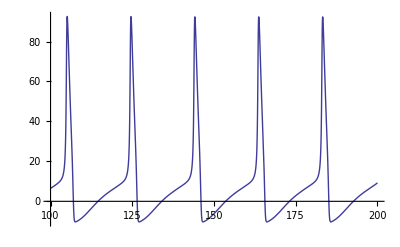

```mathematica
(* ic_case=0 *)

I1ext0[t_]:=6.27*g0[1/10 (t-0.1)];
T0=200;
sl0=SimuHHcurrent[I1ext0,T0];
tb=Table[Evaluate[V1[stv (j-2*simudt)]/.sl0],{j,1,80}];
Plot[Evaluate[V1[t]/.sl0]-0.00027756626542950875,{t,100,T0},PlotRange->All]
```

```mathematica
s1=t/.FindRoot[Evaluate[V1[t]/.sl0]==0,{t,146}]
s2=t/.FindRoot[Evaluate[V1[t]/.sl0]==0,{t,165}]
(* Slowest possible ISI, and firing rate *)
s2-s1
1000/(s2-s1)
```

146.027

165.574

19.5467

51.1594

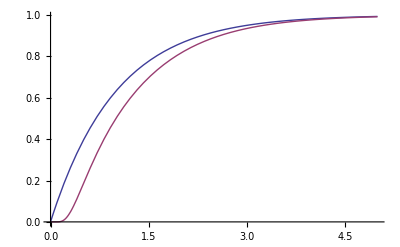

```mathematica
Plot[{g0[t],g1[t]},{t,0,5},PlotRange->All]
```

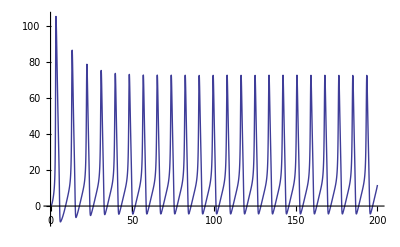

```mathematica
(* ic_case=0 *)

I1ext0[t_]:=50*g0[1/10 (t-0.1)];
T0=200;
sl0=SimuHHcurrent[I1ext0,T0];
tb=Table[Evaluate[V1[stv (j-2*simudt)]/.sl0],{j,1,80}];
Plot[Evaluate[V1[t]/.sl0]-0.00027756626542950875,{t,0,T0},PlotRange->All]
```

```mathematica
s1=t/.FindRoot[Evaluate[V1[t]/.sl0]==0,{t,169}]
s2=t/.FindRoot[Evaluate[V1[t]/.sl0]==0,{t,178}]
(* Slowest possible ISI, and firing rate *)
s2-s1
1000/(s2-s1)
```

169.595

178.139

8.5446

117.033

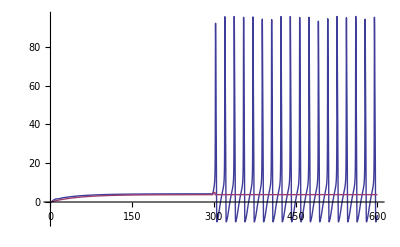

```mathematica
(* critical current input that firing will automatically disappeared *)
I1ext0[t_]:=6.264;
(* critical current input that keep the system not firing *)
I1ext0[t_]:=9.8*g0[1/50 (t-0.1)];
I1ext0[t_]:=7*g0[1/50 (t-0.1)]+2UnitBox[1/4 (t-300)];
T0=600;
sl0=SimuHHcurrent[I1ext0,T0];
tb=Table[Evaluate[V1[stv (j-2*simudt)]/.sl0],{j,1,80}];
Plot[{Evaluate[V1[t]/.sl0]-0.00027756626542950875,0.5422 I1ext0[t]},{t,0,T0},PlotRange->All]
```